```mathematica
f[x_]:=Exp[-r*x^2]
```

```mathematica
D[f[x],x]
```

-2 ⅇ^(-r x^2) r x

```mathematica
D[f[x],{x,2}]
```

-2 ⅇ^(-r x^2) r+4 ⅇ^(-r x^2) r^2 x^2

```mathematica
D[f[x],{x,3}]
```

12 ⅇ^(-r x^2) r^2 x-8 ⅇ^(-r x^2) r^3 x^3

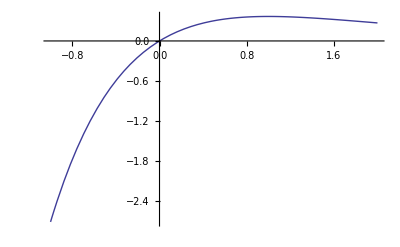

```mathematica
f[x_]:=x*Exp[-x]
Plot[f[x],{x,-1,2}]
```

```mathematica
g[x_,t_]:=(x-t)*Exp[-r(x-t)^2]
D[g[x,t],{x}]
```

ⅇ^(-r (-t+x)^2)-2 ⅇ^(-r (-t+x)^2) r (-t+x)^2

```mathematica
Simplify[ⅇ^(-r (-t+x)^2)-2 ⅇ^(-r (-t+x)^2) r (-t+x)^2]
```

ⅇ^(-r (t-x)^2) (1-2 r (t-x)^2)

```mathematica
t = Range[0,1,1/10]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

linearmesh[0,1,11]

```mathematica
c = RandomReal[{-2,2},11]
```

{1.33732,-1.1708,-1.71771,-1.76429,-0.525631,-1.11677,-0.328675,-1.9731,1.34021,-0.215252,0.894096}

t=linearmesh[0,1,11]

```mathematica
h[x_]:=Sum[c[[i]]*(1-2(x-t[[i]])^2)*Exp[-(x-t[[i]])^2],{i,11}]
```

```mathematica
h[1]
```

-0.273866

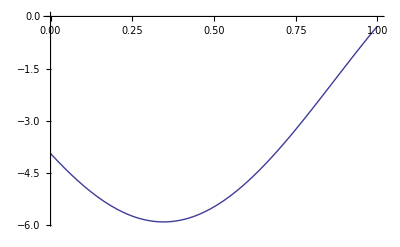

```mathematica
Plot[h[x],{x,0,1}]
```